## myPackage

```mathematica
(*erstellt am 2025-05-03*)
(*CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]
  *)

myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits = TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]]
Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}]

myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}]

Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]

myExportFigureList={};
myExportEquationList={};

impPath = Directory[] ~~ "\\Desktop\\Mathematica\\Quelle\\" (*Import-Pfad anpassen*)
exPath = Directory[] ~~ "\\Desktop\\Mathematica\\Ausgabe\\" (*Export-Pfad anpassen*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\Versionsverlauf\\" (*Pfad für Versionsverlauf*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/Versionsverlauf.nb"]]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

C:\Users\mona_\Desktop\Mathematica\Quelle\

C:\Users\mona_\Desktop\Mathematica\Ausgabe\

C:\Users\mona_\Desktop\Versionsverlauf\

myAroundString[l_]:=Module[{},If[Head[l]===List,(StringJoin[ToString[#1⟦1⟧]~~±~~ToString[#1⟦-1⟧]]&)/@l,(StringJoin[ToString[#1⟦1⟧]~~±~~ToString[#1⟦-1⟧]]&)[l]]]
myAroundString202512[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]
myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~StringReplace[ToString[i],.→]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,Rasterize[g,ImageResolution→20]}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Grid[Prepend[myExportFigureList,{ID ,figure name,preview}]]];myExportFigureList>>exPath~~myExportFigureList.m;Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotSequence[]:=Sequence[ImageSize→Large,Frame→True,myFrameStyle[],myFrameTickStyle[]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myPureColors[]:={Red,Blue,Green,Orange,Cyan,Magenta,Yellow,Black}
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧,All];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧,All]&,out,{i-1}]];out]
myStringSplit202507[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]
myUnixTime[s_String]:=(Plus@@{UnixTime[FromDateString[#1]],ToExpression[.~~#2]}&)@@StringSplit[s,.]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"}
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025,026,027,028,029,030,031,032,033,034,035,036,037,038,039,040,041,042,043,044,045,046,047,048,049,050}

## regression RIP signal and lung volume

```mathematica
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]];

NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/raw-data-import-functions.nb"];

urlHead="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/20260108-01/";
```

```mathematica
dProtocolImport["20260108-01_protocol.txt"]
```

Import successful

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→686.171 s}

```mathematica
dPexaImport["20260108-01_pexa.txt","pexa"]
```

```mathematica
createTabular[]
```

C:\Users\mona_\Desktop\Mathematica\Ausgabe\data_20260108-01.m

```mathematica
Flatten[varNames][[-2]]
```

pexa_Inhale Exhale Airflow [ml/s]

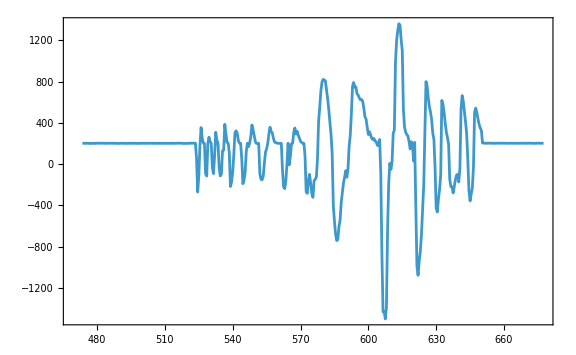

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&@Transpose[{oneTable[[1]],(oneTable[[-2]] /. "n.a."->Null)}]
```

### lung volume

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→686.171 s}

```mathematica
dRIPImport["20260108-01_rip.csv","RIP_1"]
dRIPImport["20260108-01_rip.csv","RIP_2",-2]
```

```mathematica
varNames
```

{elapsed time [s],{pexa_DeltaTime OPC [s],pexa_Particle 1 [1/L],pexa_Particle 2 [1/L],pexa_Particle 3 [1/L],pexa_Particle 4 [1/L],pexa_Particle 5 [1/L],pexa_Particle 6 [1/L],pexa_Particle 7 [1/L],pexa_Particle 8 [1/L],pexa_Particle 9 [1/L],pexa_Particle 10 [1/L],pexa_Particle 11 [1/L],pexa_Particle 12 [1/L],pexa_Particle 13 [1/L],pexa_Particle 14 [1/L],pexa_Particle 15 [1/L],pexa_Particle 16 [1/L],pexa_Particle Sum [1/L],pexa_Accumulated mass [ng],pexa_Accumulated volume [l],pexa_Exhale Counter [1],pexa_Event Counter [1],pexa_Internal Temperature [Celsius],pexa_Internal Humidity [percent],pexa_Temperature too low [1],pexa_Temperature too high [1],pexa_Circuit Flow [ml/s],pexa_Temperature Impactor [Celsius],pexa_Temperature Reservoir [Celsius],pexa_Inhale Airflow [ml/s],pexa_Inhale Exhale Airflow [ml/s],pexa_Volume [ml]},RIP_1 force ribcage [N],RIP_2 force ribcage [N]}

```mathematica
createTabular[]
```

C:\Users\mona_\Desktop\Mathematica\Ausgabe\data_20260108-01.m

```mathematica
oneTableTab[[All,"RIP_1 force ribcage [N]"]] //Normal
```

{Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,5949.93 N,5848.75 N,5747.81 N,5646.59 N,5545.28 N,5444.29 N,5343.24 N,5242.74 N,5142.64 N,5042.01 N,4940.97 N,4840.45 N,4739.73 N,4638.31 N,4536.81 N,4435.3 N,4334.1 N,4232.72 N,4131.47 N,4030.08 N,3928.98 N,3828. N,3727.21 N,3626.2 N,3525.08 N,3423.62 N,3322.35 N,3221.23 N,3120. N,3019.17 N,2918.14 N,2817.2 N,2716.72 N,2616.27 N,2515.53 N,2414.46 N,2313.26 N,2212.18 N,2111.18 N,2010.43 N,1909.95 N,1809.18 N,1707.96 N,1607.16 N,1506.22 N,1404.88 N,1303.78 N,1202.5 N,1101.69 N,1001.25 N,900.323 N,799.501 N,698.957 N,597.823 N,496.445 N,395.395 N,294.353 N,193.509 N,92.6631 N,-8.47393 N,-109.514 N,-210.945 N,-312.175 N,-413.374 N,-514.166 N,-614.989 N,-715.98 N,-816.576 N,-917.748 N,-1019.13 N,-1119.99 N,-1220.86 N,-1321.86 N,-1422.34 N,-1523.31 N,-1624.29 N,-1724.91 N,-1825.73 N,-1926.79 N,-2027.91 N,-2129.07 N,-2230.15 N,-2330.83 N,-2431.81 N,-2533.07 N,-2634.44 N,-2736.21 N,-2837.54 N,-2938.72 N,-3039.4 N,-3140.2 N,-3241.06 N,-3341.34 N,-3441.64 N,-3542.45 N,-3643.91 N,-3745.32 N,-3846.75 N,-3948.08 N,-4049.49 N,-4150.92 N,-4237.73 N,-4164.13 N,-4063.25 N,-4068.26 N,-4219.81 N,-4371.06 N,-4482.54 N,-4583.26 N,-4627.73 N,-4551.87 N,-4573.65 N,-4696.38 N,-4815.22 N,-4919.06 N,-4971.67 N,-4931.56 N,-4911.37 N,-5024.7 N,-5165.46 N,-5271.31 N,-5325.6 N,-5279.38 N,-5222.22 N,-5236.57 N,-5281.2 N,-5430.27 N,-5603.74 N,-5727.73 N,-5829.6 N,-5924.68 N,-5880.66 N,-5780.08 N,-5720.58 N,-5712.01 N,-5817.28 N,-5987.68 N,-6141.33 N,-6274.95 N,-6379.78 N,-6480.99 N,-6564.33 N,-6514.5 N,-6424.66 N,-6364.57 N,-6375.57 N,-6460.23 N,-6555.56 N,-6646.8 N,-6753.2 N,-6929.64 N,-7106.81 N,-7260.27 N,-7385.13 N,-7487.77 N,-7588.01 N,-7688.52 N,-7730.09 N,-7656.25 N,-7583.56 N,-7512.64 N,-7478.12 N,-7507.43 N,-7575.62 N,-7672.08 N,-7787.53 N,-7958.85 N,-8126.28 N,-8282.1 N,-8421.85 N,-8536.44 N,-8642.31 N,-8745.74 N,-8847.29 N,-8947.82 N,-9048.71 N,-9149.65 N,-9212.66 N,-9122.98 N,-9008.44 N,-8901.49 N,-8862.15 N,-8916.29 N,-8969.38 N,-8968.03 N,-9048.18 N,-9148.92 N,-9268.01 N,-9443.37 N,-9600.44 N,-9750.85 N,-9906.88 N,-10037.2 N,-10154.5 N,-10261.7 N,-10365. N,-10465.8 N,-10556.1 N,-10494.1 N,-10351.2 N,-10234.1 N,-10181.9 N,-10113. N,-9992.58 N,-9831.8 N,-9713.2 N,-9638.54 N,-9573.46 N,-9526.98 N,-9662.39 N,-9902.42 N,-10218.3 N,-10597.2 N,-11002.5 N,-11412.5 N,-11821.7 N,-12202.2 N,-12539.6 N,-12837.7 N,-13065.8 N,-13240.3 N,-13356.7 N,-13266.2 N,-13035.5 N,-12727.2 N,-12367.4 N,-11993.9 N,-11660.6 N,-11372. N,-11138.9 N,-10982.9 N,-10865.6 N,-10786.1 N,-10748. N,-10698.1 N,-10650.8 N,-10676.4 N,-10781.9 N,-10978.9 N,-11286.7 N,-11683.9 N,-12068.8 N,-12441.8 N,-12799.2 N,-13135.9 N,-13465.2 N,-13777.1 N,-14096.2 N,-14403.9 N,-14688.8 N,-14940.6 N,-15167. N,-15365. N,-15525.5 N,-15674.9 N,-15824.6 N,-15959.3 N,-16079.2 N,-16198.6 N,-16317.9 N,-16429.7 N,-16526.2 N,-16618.4 N,-16722.4 N,-16793.3 N,-16574.8 N,-15947.2 N,-15240.6 N,-14506.3 N,-13765.8 N,-13236.6 N,-13053.6 N,-13004.4 N,-13008.3 N,-12981.6 N,-13074.6 N,-13218.7 N,-13564.4 N,-14096.1 N,-14729.9 N,-15390.8 N,-16074.7 N,-16721.5 N,-17291.9 N,-17714.4 N,-17928.5 N,-18093.7 N,-18241.5 N,-18381.4 N,-18503.4 N,-18611.8 N,-18682.9 N,-18793.4 N,-18868. N,-18912.6 N,-18893.4 N,-18535. N,-17989.3 N,-17490.5 N,-17043.5 N,-16657.2 N,-16373.1 N,-16212.9 N,-16203.5 N,-16509. N,-16909.7 N,-17257.9 N,-17556.8 N,-17821.4 N,-18060.4 N,-18241.1 N,-18373.4 N,-18457.3 N,-18325. N,-18088.7 N,-17888.2 N,-17744.6 N,-17638.7 N,-17771. N,-18085.4 N,-18355.7 N,-18580.6 N,-18757.3 N,-18898.3 N,-19022.3 N,-19025.7 N,-18933.5 N,-18823.8 N,-18701. N,-18569.6 N,-18480.6 N,-18414.9 N,-18370.9 N,-18297.1 N,-18225.7 N,-18355.1 N,-18654.7 N,-18981.5 N,-19259.1 N,-19491.3 N,-19666.9 N,-19769. N,-19704. N,-19537.9 N,-19379.3 N,-19247.9 N,-19161.4 N,-19293.9 N,-19563.8 N,-19825.8 N,-20061.1 N,-20266.7 N,-20449.8 N,-20618.8 N,-20764.2 N,-20854.6 N,-20956.7 N,-21057.9 N,-21159.1 N,-21260.5 N,-21361.9 N,-21463.7 N,-21565.2 N,-21666.4 N,-21767.3 N,-21868.2 N,-21969.5 N,-22070.8 N,-22172.5 N,-22273.8 N,-22375.4 N,-22476.8 N,-22578.4 N,-22679.9 N,-22781.6 N,-22882.8 N,-22984.2 N,-23085.2 N,-23186.4 N,-23287.5 N,-23388.8 N,-23490.1 N,-23591.2 N,-23692.4 N,-23793.6 N,-23894.3 N,-23995.4 N,-24096.5 N,-24197.7 N,-24299.3 N,-24400.7 N,-24502.1 N,-24603.2 N,-24704.3 N,-24805.5 N,-24906.6 N,-25008.4 N,-25109.8 N,-25211.1 N,-25312. N,-25412.8 N,-25513.8 N,-25615. N,-25716.6 N,-25818.2 N,-25919.4 N,-26020.8 N,-26121.8 N,-26202.9 N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N,Missing[] N}

```mathematica
oneTable[[-1]]
```

{n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,3.63761,6.15429,8.02029,5.00198,3.10873,2.36522,2.30049,2.25024,2.80468,4.15883,4.76692,3.75259,2.71866,2.48531,2.71781,3.46387,2.29453,1.05962,0.467707,0.170479,0.0299505,-0.0926895,-0.0484034,-0.00837708,-0.0160421,-0.154007,0.183253,0.0427246,-0.0969493,0.494965,0.69766,1.22825,0.882469,0.0963821,-0.156563,-0.00582123,4.97728,5.82725,12.5188,27.7645,53.0743,66.7589,41.9711,16.8444,10.8878,7.63363,6.90971,6.6474,10.2193,15.3216,13.2972,8.41035,7.06131,6.99488,7.55102,10.6306,14.9639,17.2583,11.8962,8.71184,7.62085,5.26003,4.70731,4.23293,3.79346,3.57884,3.90589,4.20226,4.56678,4.6775,4.28147,4.27636,4.10432,3.87778,4.69879,5.07352,4.27636,3.59418,3.71767,2.95287,3.70234,3.71681,4.83506,13.8065,44.142,73.2179,78.603,80.6121,63.0609,25.6464,11.3162,6.87991,6.63292,7.20695,7.50758,7.62852,7.13796,6.38679,7.25293,8.39502,8.4095,7.02043,6.01546,6.35102,10.7107,13.5433,9.22454,7.3858,7.15159,7.19928,7.07749,6.98721,7.07664,7.1814,9.87436,15.2501,16.0728,12.5418,8.55428,7.09963,11.5419,17.8076,14.0748,10.9219,9.80112,8.44101,7.91468,8.03732,7.67792,8.51511,12.2539,14.1208,9.65123,7.33981,7.21972,7.42156,11.369,15.2322,13.626,7.976,7.02469,6.85435,7.16351,9.73129,17.243,23.467,18.9114,16.456,11.467,7.55187,6.50773,6.10319,9.88374,16.7754,14.2707,11.7216,10.2883,8.4129,6.49154,7.31937,10.8197,12.4089,9.10957,8.71184,10.3249,18.6661,15.5848,10.9705,10.514,9.97401,16.8419,11.6578,13.3653,16.6502,8.87791,5.8809,5.08204,3.90333,4.1418,5.94478,6.28033,4.85123,4.08985,3.66316,3.4281,4.86146,9.55755,8.37969,4.47906,3.84457,7.65918,7.97344,6.32462,7.8457,13.4727,13.4514,9.93058,6.81603,5.19872,5.11696,7.3628,9.43746,7.98963,7.10474,18.4702,14.8566,11.5189,18.6585,19.9445,12.3118,8.60623,9.17941,16.7286,14.9818,11.8332,8.98012,9.33441,14.1182,12.0223,10.904,9.72447,16.571,19.0945,27.4834,18.5733,10.0174,19.0988,25.6157,16.0949,10.3649,8.35499,8.10886,11.1655,9.49622,6.24882,5.16295,8.11993,8.71951,5.31454,4.05663,11.7583,17.3145,9.17515,9.16408,17.7097,15.9042,10.2585,7.1073,5.6782,5.09396,4.5753,3.66827,6.25052,8.43079,6.01887,4.79247,4.03278,4.39133,7.8491,8.12675,5.07778,4.2227,4.0643,4.00553,4.39985,5.932,6.04612,4.44755,4.30787,3.94676,4.25762,5.58196,6.50091,4.81036,4.14179,3.80369,4.47906,6.50943,6.34762,4.7056,3.98424,3.88544,4.0413,5.69439,6.85691,5.50787,4.20482,3.67338,4.25933,6.53754,7.15414,5.05308,3.94166,3.26969,5.16039,7.42667,5.87238,4.36323,3.87863,3.62994,6.28544,7.50077,3.47239,2.56451,6.39871,10.9321,6.48559,3.98254,4.14009,7.75372,8.28686,5.5232,4.56934,5.13484,7.79971,7.61575,5.40908,4.56763,4.66217,6.93356,7.83122,6.04186,4.88956,4.43477,5.22001,8.0782,8.30048,5.53087,4.52164,4.35301,7.17884,6.96422,4.41263,3.46642,3.3276,4.23548,6.37231,5.52831,4.13328,3.48176,3.52434,5.10929,6.69254,5.52065,3.98765,3.46898,3.53626,5.18083,6.30077,4.90745,3.87012,3.18282,4.14861,6.2616,6.37998,4.35557,3.5567,3.20326,4.85294,6.56053,5.38097,3.75259,3.28247,5.16295,7.26486,5.38268,3.77728,3.10873,5.01135,7.83037,6.36209,4.32491,3.0721,3.66572,6.48899,7.36024,5.33754,3.42299,4.63576,7.90957,7.05961,3.66572,3.4792,3.83434,5.37671,5.9831,4.35982,3.42299,4.4731,6.98977,7.02128,4.91256,3.92547,3.55585,5.55812,7.0562,5.42185,4.03364,3.81816,4.7567,7.06642,7.0562,5.01646,3.97231,3.63846,4.69283,6.48899,6.38424,4.53442,3.65805,4.38452,7.13796,6.84073,3.08318,2.46316,3.11894,6.61078,6.44044,3.91696,2.5313,3.00142,5.64073,6.10234,4.1665,3.14024,2.90944,5.51042,7.02043,4.36579,3.05251,3.75599,6.63973,7.15925,4.51653,3.86926,4.49354,9.2024,9.77472,6.70702,5.12206,6.33313,10.3189,11.3324,8.46656,6.19261,5.30602,5.78211,8.4129,8.91113,6.4941,5.4193,4.66472,5.3188,7.98367,9.27138,6.98721,5.72675,5.15784,5.63136,8.22894,9.88459,9.21517,8.70333,10.0915,14.5517,13.505,8.42994,7.34747,8.63689,10.0481,7.9019,5.61007,5.62285,7.62086,9.54307,7.6924,6.05549,7.58253,12.0631,12.5724,13.3117,17.2711,11.6441,13.0451,13.4871,9.45023,7.79459,7.47522,12.9157,10.6025,7.0051,7.5442,13.2836,10.0864,7.17714,8.99289,9.57628,13.39,9.55499,8.13696,9.80794,5.74804,7.27934,15.8556,20.9588,17.6876,21.5865,20.0075,9.50304,6.22582,11.1502,11.3409,19.8585,24.2999,15.5414,14.9077,15.4179,11.2362,8.12164,5.99843,11.616,13.4641,7.77245,6.38424,9.62142,11.5786,7.6694,5.56919,10.014,13.0809,20.2051,16.1597,9.99956,11.8954,13.9309,8.42824,7.05109,12.8024,8.93498,5.6254,8.47252,14.757,11.1263,7.48289,6.20113,5.69694,7.90361,10.3905,7.96152,5.64073,4.63321,5.84258,8.84725,7.7716,5.5232,4.52164,5.47721,8.55087,8.9946,6.88246,5.2166,5.6484,10.1503,11.019,6.75216,4.95599,5.49595,9.16408,10.313,7.40368,5.7557,4.85123,8.02199,13.7784,14.3431,11.6475,8.69481,5.36735,4.75159,8.70162,10.3198,6.76749,5.64754,5.38268,9.33952,12.2147,7.88913,5.42355,5.10418,6.97955,9.77728,8.43845,5.9073,5.05819,6.41404,9.36081,8.85066,6.56053,5.29921,5.57686,8.75101,10.531,7.42156,5.46699,5.54279,7.7486,10.2023,8.51511,6.45322,5.63051,8.48359,11.8673,9.1777,6.25137,5.55131,8.73483,12.1653,9.52177,6.43874,5.36224,7.38324,10.8197,9.18366,5.87324,5.0897,5.38268,6.99232,12.529,7.34662,4.77203,9.27735,11.9005,6.42086,9.96635,12.8382,8.5611,6.05635,7.98111,12.3868,10.9628,5.97203,6.48132,14.4189,14.4708,11.4406,16.4816,17.0352,12.713,8.59772,12.9225,15.9459,12.9583,11.1357,8.93157,6.05635,3.82413,5.86472,7.17628,4.18864,3.59673,7.15244,10.1018,7.65407,6.03676,4.85379,4.13328,5.9797,7.16096,5.69183,4.73115,4.36408,4.91511,10.026,16.4433,14.47,7.6413,5.68842,4.86146,4.53101,6.5452,10.2934,11.2234,7.30233,5.41589,4.85294,5.87068,9.64016,12.7615,8.71099,4.92789,4.04215,5.0863,8.01262,13.1294,15.7645,16.5097,8.50063,4.97388,3.96635,3.53541,4.03789,7.52377,15.4332,21.8343,23.1587,16.5582,9.08061,5.21404,4.12391,3.30035,3.13257,3.99531,7.78097,14.6803,20.6573,24.1057,25.9402,28.4262,29.243,26.5534,15.2296,7.01532,5.01561,4.20993,4.0396,4.18694,4.16564,5.21149,9.28075,16.5761,26.2971,33.4212,36.5349,40.1358,39.1666,31.2112,19.2708,10.7712,6.48643,4.66727,3.86586,3.51241,2.92476,2.74592,2.55089,2.66415,2.97076,4.05408,8.42057,18.3212,30.5733,37.0212,39.1419,42.9284,47.0241,50.3328,47.5393,36.569,22.8504,14.5475,9.04314,5.53597,4.68431,4.23804,3.73896,3.19559,3.29183,3.96721,9.02611,18.6866,30.1134,35.7642,39.9689,43.5135,47.696,51.6435,56.1497,60.1159,57.7091,46.4696,38.1727,28.6817,19.046,11.065,6.82029,5.23449,4.42029,3.67849,2.98523,2.07651,1.98793,2.26302,4.0643,5.57686,8.23746,14.1387,22.6894,31.1601,40.5616,50.0875,57.1844,64.0787,66.0222,67.2546,69.313,70.111,66.4881,61.2477,52.7754,39.7065,25.8286,16.6988,11.5845,7.50333,6.09467,5.13484,4.37771,3.29524,2.41036,1.35088,0.899503,0.74791,0.866287,0.954865,0.948049,1.09028,1.08942,1.0545,0.913981,0.913979,0.854365,0.7939,0.84244,0.908875,0.999997,3.1496,10.6724,23.3903,44.4478,72.5613,80.831,81.1921,81.1921,81.1921,81.1921,81.1921,74.6291,49.832,29.622,14.412,8.80212,4.10518,1.45479,0.622711,0.967636,1.00851,0.885022,0.819443,0.547765,0.443863,0.626119,0.954865,1.20695,1.31001,1.19077,0.60994,1.70262,4.39389,9.25521,15.7406,22.6161,28.554,30.7564,28.0609,19.1098,11.6194,7.51951,5.91923,5.30773,4.71326,4.17586,4.16394,4.27125,5.84513,9.13001,12.4626,14.5977,16.0217,12.0052,7.27593,5.99076,5.56408,5.06245,5.00964,4.90063,5.04286,6.11852,7.35258,9.62312,11.8673,13.5595,14.6956,15.5703,17.0309,17.4627,14.1872,8.87451,5.94478,5.14506,4.65195,4.22356,4.26869,4.98069,6.67806,9.44087,11.668,12.4379,9.41958,7.07409,5.59219,4.82057,3.93143,3.42725,3.03463,2.99631,4.54208,7.67451,9.5882,9.1496,7.98622,9.24158,9.05932,9.44172,10.0992,7.40198,5.15528,12.3084,13.6941,9.96464,9.26627,9.29523,9.70829,9.55925,9.31482,9.06869,8.42824,9.4102,9.08231,6.45066,8.35159,11.3341,13.482,13.3517,12.9174,8.86003,7.57231,7.49055,7.39346,7.23931,7.05109,6.97274,6.6985,7.39942,10.5259,10.749,7.42923,6.48729,6.64996,6.99914,6.63207,8.01347,12.0793,10.0702,7.11752,6.98125,8.87536,9.99871,7.78948,9.8173,8.74506,7.3347,6.72661,5.52065,4.64172,5.61092,9.12319,10.7592,7.34747,6.62185,n.a.,n.a.,n.a.}

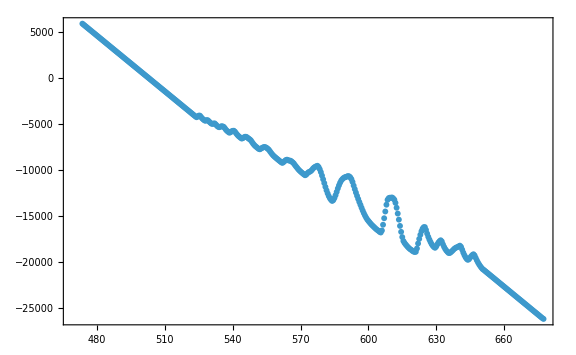

```mathematica
ListPlot[oneTableTab->{"elapsed time [s]","RIP_1 force ribcage [N]"},myPlotSequence[],PlotRange->All]
```

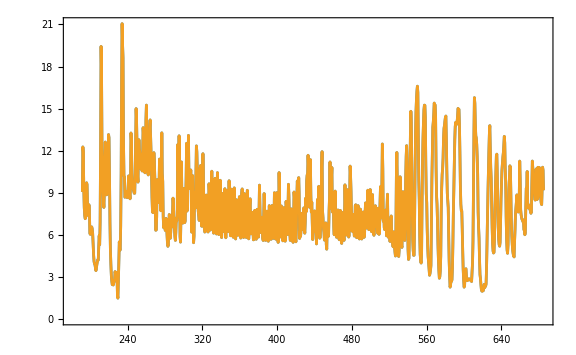

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&@({Transpose[{oneTable[[1]],(oneTable[[-2]] /. "n.a."->Null)}],Transpose[{oneTable[[1]],oneTable[[-2]] }]}/. "n.a."->Null)
```

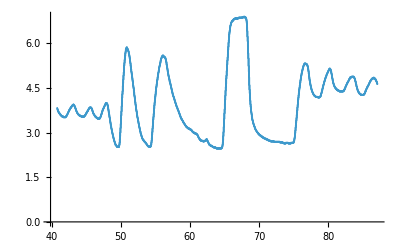
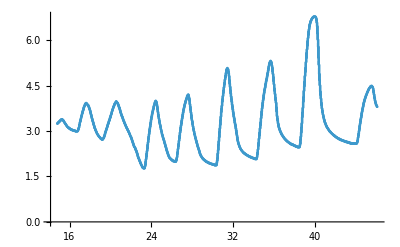
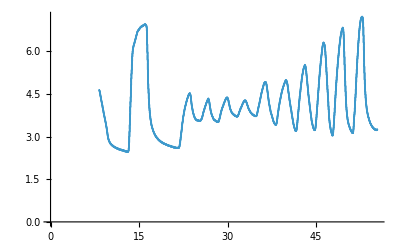
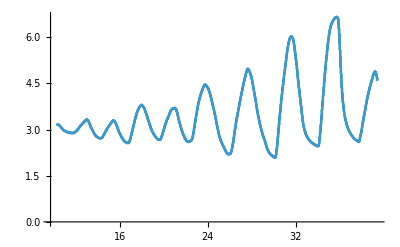
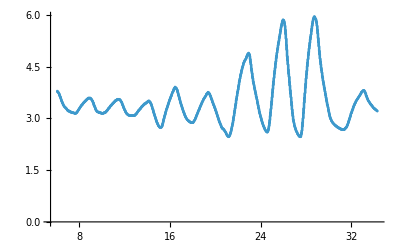
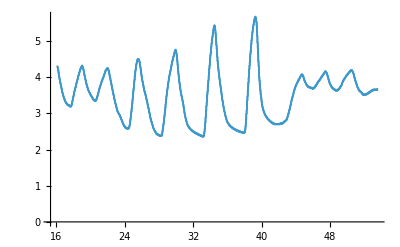
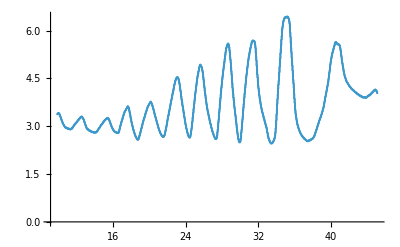
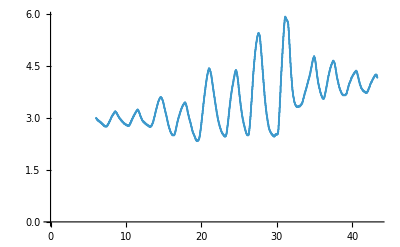

```mathematica
spiroTimeDeltaCorrection=.
spiroTimeDeltaCorrection[list_List]:=Module[{diff,lasttime,temp,tempAll},
Map[(lasttime=#[[2,-1,1]];
diff=#[[1]]-lasttime;
temp=#[[2,All,1]]+diff;
tempAll=#;
tempAll[[2,All,1]]=temp;
#[[-1]]->tempAll[[2]]
)&
,list
]
]

spiroDataTimeCalibrated=spiroTimeDeltaCorrection[Transpose[{times[[parts]][[All,-2]],points,filenames[[parts]]}]];
ListPlot[#[[2]]]&/@spiroDataTimeCalibrated
```

```mathematica
Abs[Subtract@@MinMax@#[[2,All,2]]] &/@spiroDataTimeCalibrated
```

{4.44068,5.01695,4.76271,4.59322,3.49153,3.32203,3.98305,3.59322}

```mathematica
spiroDataTimeCalibrated
```

```mathematica
smoothSpiroData=.
smoothSpiroData[l_]:=l[[1]]->((Normal[Mean[#[[All,2]]]&/@GroupBy[l[[2]],First]]) /. (Rule->List))

spiroDataTimeCalibratedSmoothed=smoothSpiroData[#]&/@spiroDataTimeCalibrated
```

### RIP data

```mathematica
allRIPData=(path="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/"~~#~~".csv";If[URLRead[path]["StatusCode"]==200,#->Import[path],Nothing])&/@filenames
```

```mathematica
TableForm[allRIPData[[-1,2,1;;5]]] (*die Datensätze wurden beim Export vom Vernier Programm zusammengehängt. Der letzte Datensatz enthält alle Messreihen!*)
```

Datensatz 1:Zeit(s) | Datensatz 1:Force 1(N) | Datensatz 1:Respiration Rate 1(bpm) | Datensatz 1:Force 2(N) | Datensatz 1:Respiration Rate 2(bpm) | Datensatz 2:Zeit(s) | Datensatz 2:Force 1(N) | Datensatz 2:Respiration Rate 1(bpm) | Datensatz 2:Force 2(N) | Datensatz 2:Respiration Rate 2(bpm) | Datensatz 3:Zeit(s) | Datensatz 3:Force 1(N) | Datensatz 3:Respiration Rate 1(bpm) | Datensatz 3:Force 2(N) | Datensatz 3:Respiration Rate 2(bpm) | Datensatz 4:Zeit(s) | Datensatz 4:Force 1(N) | Datensatz 4:Respiration Rate 1(bpm) | Datensatz 4:Force 2(N) | Datensatz 4:Respiration Rate 2(bpm) | Datensatz 5:Zeit(s) | Datensatz 5:Force 1(N) | Datensatz 5:Respiration Rate 1(bpm) | Datensatz 5:Force 2(N) | Datensatz 5:Respiration Rate 2(bpm) | Datensatz 6:Zeit(s) | Datensatz 6:Force 1(N) | Datensatz 6:Respiration Rate 1(bpm) | Datensatz 6:Force 2(N) | Datensatz 6:Respiration Rate 2(bpm) | Datensatz 7:Zeit(s) | Datensatz 7:Force 1(N) | Datensatz 7:Respiration Rate 1(bpm) | Datensatz 7:Force 2(N) | Datensatz 7:Respiration Rate 2(bpm) | Datensatz 8:Zeit(s) | Datensatz 8:Force 1(N) | Datensatz 8:Respiration Rate 1(bpm) | Datensatz 8:Force 2(N) | Datensatz 8:Respiration Rate 2(bpm) | Datensatz 9:Zeit(s) | Datensatz 9:Force 1(N) | Datensatz 9:Respiration Rate 1(bpm) | Datensatz 9:Force 2(N) | Datensatz 9:Respiration Rate 2(bpm) | Datensatz 10:Zeit(s) | Datensatz 10:Force 1(N) | Datensatz 10:Respiration Rate 1(bpm) | Datensatz 10:Force 2(N) | Datensatz 10:Respiration Rate 2(bpm) | Datensatz 11:Zeit(s) | Datensatz 11:Force 1(N) | Datensatz 11:Respiration Rate 1(bpm) | Datensatz 11:Force 2(N) | Datensatz 11:Respiration Rate 2(bpm) | Datensatz 12:Zeit(s) | Datensatz 12:Force 1(N) | Datensatz 12:Respiration Rate 1(bpm) | Datensatz 12:Force 2(N) | Datensatz 12:Respiration Rate 2(bpm) | Datensatz 13:Zeit(s) | Datensatz 13:Force 1(N) | Datensatz 13:Respiration Rate 1(bpm) | Datensatz 13:Force 2(N) | Datensatz 13:Respiration Rate 2(bpm) | Datensatz 14:Zeit(s) | Datensatz 14:Force 1(N) | Datensatz 14:Respiration Rate 1(bpm) | Datensatz 14:Force 2(N) | Datensatz 14:Respiration Rate 2(bpm) | Datensatz 15:Zeit(s) | Datensatz 15:Force 1(N) | Datensatz 15:Respiration Rate 1(bpm) | Datensatz 15:Force 2(N) | Datensatz 15:Respiration Rate 2(bpm) | Datensatz 16:Zeit(s) | Datensatz 16:Force 1(N) | Datensatz 16:Respiration Rate 1(bpm) | Datensatz 16:Force 2(N) | Datensatz 16:Respiration Rate 2(bpm) | Datensatz 17:Zeit(s) | Datensatz 17:Force 1(N) | Datensatz 17:Respiration Rate 1(bpm) | Datensatz 17:Force 2(N) | Datensatz 17:Respiration Rate 2(bpm) | Datensatz 18:Zeit(s) | Datensatz 18:Force 1(N) | Datensatz 18:Respiration Rate 1(bpm) | Datensatz 18:Force 2(N) | Datensatz 18:Respiration Rate 2(bpm) | Datensatz 19:Zeit(s) | Datensatz 19:Force 1(N) | Datensatz 19:Respiration Rate 1(bpm) | Datensatz 19:Force 2(N) | Datensatz 19:Respiration Rate 2(bpm)
0. | 14.8856 | 22.3729 | 12.2965 | 22.3577 | 0. | 10.5293 | 21.398 | 8.47167 | 21.4133 | 0. | 12.8084 | 20.7612 | 10.1018 | 20.7756 | 0. | 14.3618 | 0. | 10.9091 | 14.4578 | 0. | 16.2346 | 22.0147 | 11.2106 | 18.012 | 0. | 12.5554 | 21.9619 | 8.96478 | 21.9619 | 0. | 10.3147 | 9.91736 | 8.25705 | 9.90099 | 0. | 10.7439 | 16.632 | 9.34293 | 14.5935 | 0. | 10.0387 | 20.3313 | 7.38835 | 20.4255 | 0. | 11.2626 | 21.2598 | 7.75627 | 20.2551 | 0. | 12.6704 | 12.5174 | 8.97756 | 12.4138 | 0. | 10.5651 | 0. | 7.99644 | 0. | 0. | 12.3331 | 0 | 9.44768 | 19.4384 | 0. | 8.64626 | 0. | 7.12774 | 19.4085 | 0. | 9.85989 | 6.23701 | 7.5672 | 0 | 0. | 7.91808 | 6.85453 | 6.67551 | 14.7472 | 0. | 12.2999 | 8.79765 | 8.49467 | 17.2579 | 0. | 10.7541 | 21.7077 | 7.83037 | 20.0267 | 0. | 7.17203 | 0. | 6.34846 | 8.44278
0.1 | 13.9734 | Missing[NotAvailable] | 11.7421 | Missing[NotAvailable] | 0.1 | 11.5896 | Missing[NotAvailable] | 9.11553 | Missing[NotAvailable] | 0.1 | 11.4798 | Missing[NotAvailable] | 9.38636 | Missing[NotAvailable] | 0.1 | 12.6985 | Missing[NotAvailable] | 9.93568 | Missing[NotAvailable] | 0.1 | 16.7405 | Missing[NotAvailable] | 11.4252 | Missing[NotAvailable] | 0.1 | 14.1318 | Missing[NotAvailable] | 9.93313 | Missing[NotAvailable] | 0.1 | 9.73213 | Missing[NotAvailable] | 8.06032 | Missing[NotAvailable] | 0.1 | 9.45109 | Missing[NotAvailable] | 8.49722 | Missing[NotAvailable] | 0.1 | 11.679 | Missing[NotAvailable] | 8.25705 | Missing[NotAvailable] | 0.1 | 10.7107 | Missing[NotAvailable] | 7.79971 | Missing[NotAvailable] | 0.1 | 11.237 | Missing[NotAvailable] | 8.55598 | Missing[NotAvailable] | 0.1 | 11.0837 | Missing[NotAvailable] | 8.11141 | Missing[NotAvailable] | 0.1 | 11.5462 | Missing[NotAvailable] | 8.95712 | Missing[NotAvailable] | 0.1 | 8.19658 | Missing[NotAvailable] | 6.81603 | Missing[NotAvailable] | 0.1 | 9.47408 | Missing[NotAvailable] | 7.2376 | Missing[NotAvailable] | 0.1 | 7.59104 | Missing[NotAvailable] | 6.69083 | Missing[NotAvailable] | 0.1 | 13.0639 | Missing[NotAvailable] | 8.88814 | Missing[NotAvailable] | 0.1 | 9.90332 | Missing[NotAvailable] | 7.37813 | Missing[NotAvailable] | 0.1 | 7.20013 | Missing[NotAvailable] | 6.43533 | Missing[NotAvailable]
0.2 | 12.7036 | Missing[NotAvailable] | 10.9117 | Missing[NotAvailable] | 0.2 | 13.0996 | Missing[NotAvailable] | 9.97146 | Missing[NotAvailable] | 0.2 | 10.1052 | Missing[NotAvailable] | 8.67352 | Missing[NotAvailable] | 0.2 | 10.772 | Missing[NotAvailable] | 8.70928 | Missing[NotAvailable] | 0.2 | 16.7865 | Missing[NotAvailable] | 11.415 | Missing[NotAvailable] | 0.2 | 16.135 | Missing[NotAvailable] | 11.0011 | Missing[NotAvailable] | 0.2 | 9.13426 | Missing[NotAvailable] | 7.81248 | Missing[NotAvailable] | 0.2 | 8.06883 | Missing[NotAvailable] | 7.50077 | Missing[NotAvailable] | 0.2 | 13.7614 | Missing[NotAvailable] | 9.34037 | Missing[NotAvailable] | 0.2 | 10.0106 | Missing[NotAvailable] | 7.70773 | Missing[NotAvailable] | 0.2 | 9.54307 | Missing[NotAvailable] | 7.96067 | Missing[NotAvailable] | 0.2 | 11.0658 | Missing[NotAvailable] | 8.12164 | Missing[NotAvailable] | 0.2 | 10.4859 | Missing[NotAvailable] | 8.2826 | Missing[NotAvailable] | 0.2 | 7.71624 | Missing[NotAvailable] | 6.45833 | Missing[NotAvailable] | 0.2 | 9.36421 | Missing[NotAvailable] | 6.87735 | Missing[NotAvailable] | 0.2 | 7.58849 | Missing[NotAvailable] | 6.76237 | Missing[NotAvailable] | 0.2 | 13.5519 | Missing[NotAvailable] | 9.13086 | Missing[NotAvailable] | 0.2 | 8.79189 | Missing[NotAvailable] | 6.8518 | Missing[NotAvailable] | 0.2 | 7.43008 | Missing[NotAvailable] | 6.78537 | Missing[NotAvailable]
0.3 | 12.0623 | Missing[NotAvailable] | 10.4084 | Missing[NotAvailable] | 0.3 | 14.0271 | Missing[NotAvailable] | 10.393 | Missing[NotAvailable] | 0.3 | 9.91354 | Missing[NotAvailable] | 8.57642 | Missing[NotAvailable] | 0.3 | 10.4015 | Missing[NotAvailable] | 8.35414 | Missing[NotAvailable] | 0.3 | 16.02 | Missing[NotAvailable] | 11.0292 | Missing[NotAvailable] | 0.3 | 17.0292 | Missing[NotAvailable] | 11.2566 | Missing[NotAvailable] | 0.3 | 9.07294 | Missing[NotAvailable] | 7.70006 | Missing[NotAvailable] | 0.3 | 7.9513 | Missing[NotAvailable] | 7.26315 | Missing[NotAvailable] | 0.3 | 14.7604 | Missing[NotAvailable] | 9.64442 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.54676 | Missing[NotAvailable] | 0.3 | 9.11893 | Missing[NotAvailable] | 7.53654 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.88402 | Missing[NotAvailable] | 0.3 | 9.93143 | Missing[NotAvailable] | 8.03477 | Missing[NotAvailable] | 0.3 | 7.71368 | Missing[NotAvailable] | 6.48132 | Missing[NotAvailable] | 0.3 | 9.8139 | Missing[NotAvailable] | 6.93101 | Missing[NotAvailable] | 0.3 | 8.49807 | Missing[NotAvailable] | 7.03065 | Missing[NotAvailable] | 0.3 | 12.8876 | Missing[NotAvailable] | 8.87791 | Missing[NotAvailable] | 0.3 | 8.25279 | Missing[NotAvailable] | 6.72916 | Missing[NotAvailable] | 0.3 | 7.95386 | Missing[NotAvailable] | 7.32958 | Missing[NotAvailable]

```mathematica
ripData=Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,All,{1,2,4}]]}]
```

```mathematica
ripData=#[[1]]->#[[2]]&/@(Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,2;;-1,{1,2,4}]]}]/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
```

```mathematica
Transpose[{ filenames,times}]
```

{{13-52,{0.,11.587,86.626,163.838}},{13-58,{0.,10.215,87.148,96.617}},{14-07,{0.,7.21,46.161,95.607}},{14-09,{0.,6.607,55.385,76.168}},{14-12,{0.,6.155,39.394,51.1}},{14-16,{0.,4.767,34.314,45.389}},{14-18,{0.,16.13,53.533,60.223}},{14-21,{0.,5.265,45.151,69.111}},{14-25,{0.,4.027,43.35,48.236}},{14-28,{0.,4.538,32.585,48.87}},{14-30,{0.,4.698,34.442,48.932}},{14-34,{0.,18.158,64.024,77.825}}}

```mathematica
{#[[1]],#[[2,-1,1]]}&/@(ripData/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
(*die Zeiten der RIP Messungen sind "Taktgeber" und synchron*)
```

{{13-52,163.2},{13-58,95.9},{14-07,94.8},{14-09,75.5},{14-18,59.4},{14-21,68.5},{14-28,48.2},{14-30,48.1},{14-34,77.1}}

### Evaluation

```mathematica
Length@spiroDataTimeCalibratedSmoothed
Length@ripData
spiroDataTimeCalibratedSmoothed[[All,1]]
ripData[[All,1]]
evaluableData=Intersection[spiroDataTimeCalibrated[[All,1]],ripData[[All,1]]]
```

8

9

{13-58,14-07,14-09,14-12,14-16,14-18,14-21,14-25}

{13-52,13-58,14-07,14-09,14-18,14-21,14-28,14-30,14-34}

{13-58,14-07,14-09,14-18,14-21}

```mathematica
calibrateXMin=.
calibrateXMin[spiro_List]:=Module[{lowestVolumes,lowestForce}
,lowestVolumes=Min[spiro[[All,2]]]
]
calibrateXMin[spiroDataTimeCalibratedSmoothed[[-1,2]]]
```

2.33051

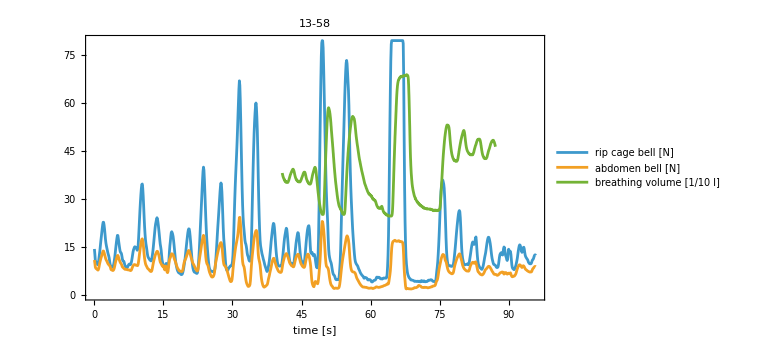
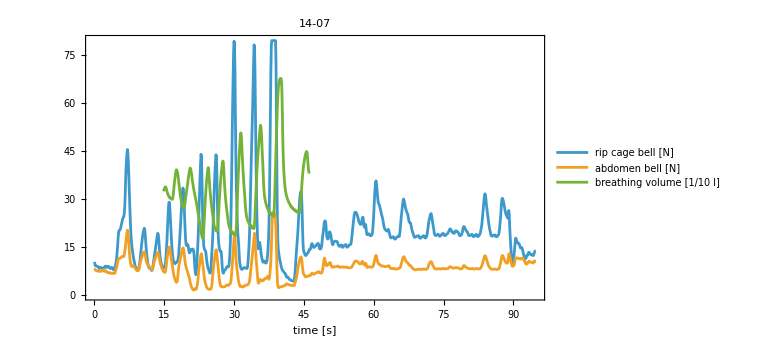
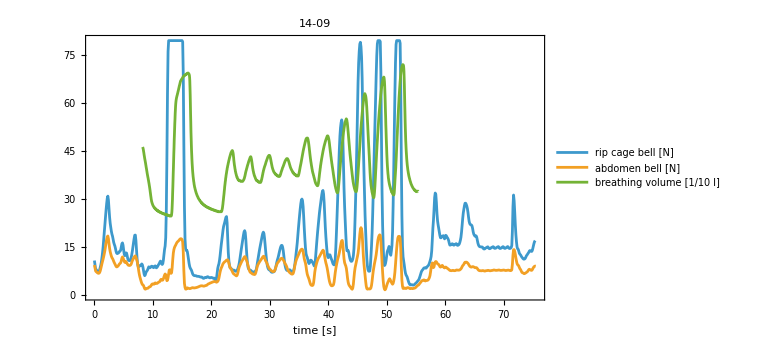
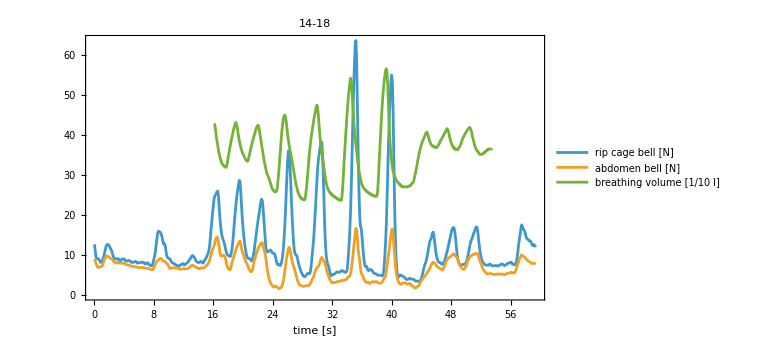
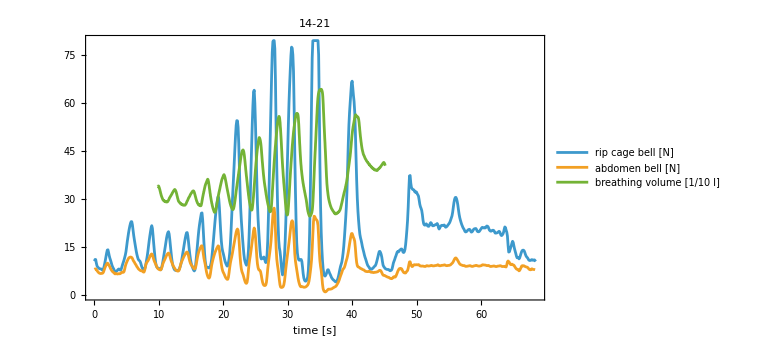

```mathematica
dataForAnalysis=Transpose[{evaluableData,evaluableData/.ripData,evaluableData /. spiroDataTimeCalibratedSmoothed}];
dataForAnalysis[[All,2]]=Map[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@(Flatten[#,1])] /. Missing["NotAvailable"]->Null&,dataForAnalysis[[All,{2}]]];

ListPlot[Append[#[[2]],{#[[1]],#[[2]]*10}&/@#[[3]]],PlotLabel->myStyle@#[[1]],PlotRange->All,PlotLegends->{"rip cage bell [N]","abdomen bell [N]","breathing volume [1/10 l]"},FrameLabel->{"time [s]",None},ImageSize->Large,Frame->True,Joined->True,myFrameStyle[],myFrameTickStyle[], myPlotStyle[]]&/@dataForAnalysis
```

```mathematica
dataForAnalysis={#[[1]],Append[#[[2]],#[[3]]]}&/@dataForAnalysis (*time stamp, {rip, abdomen, spiro}*)
```

{{{41.8813,3.51695},{43.1813,3.9322}},{{44.5147,3.5339},{45.648,3.83898}},{{46.8147,3.4661},{47.9147,3.99153}},{{49.6147,2.51695},{50.8813,5.85593}},{{54.2147,2.51695},{56.1147,5.58475}},{{64.2147,2.4661},{67.8147,6.88136}},{{74.4147,2.63559},{76.6813,5.31356}},{{78.648,4.17797},{80.248,5.14407}},{{81.9147,4.38136},{83.5813,4.87288}},{{84.9813,4.26271},{86.648,4.83898}}}

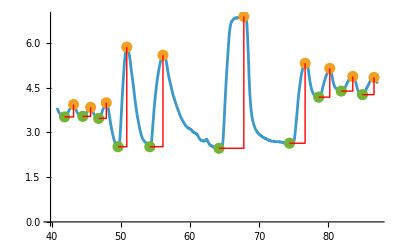

```mathematica
values=dataForAnalysis[[1,2,3]];
peaks=FindPeaks[dataForAnalysis[[1,2,3]][[All,2]],10];
peaksLow=FindPeaks[-dataForAnalysis[[1,2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}]
xdiffsLine={#[[1]],{#[[2,1]],
#[[1,2]]},#[[2]]}&/@xdiffs;
linesDiff=Line/@xdiffsLine;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}]

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All}
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
```

breaths from spirometry

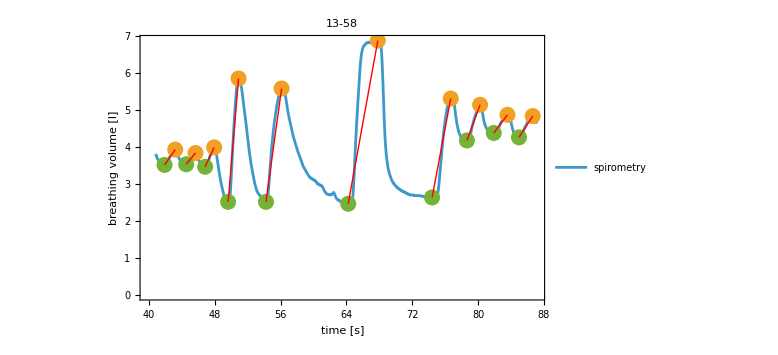
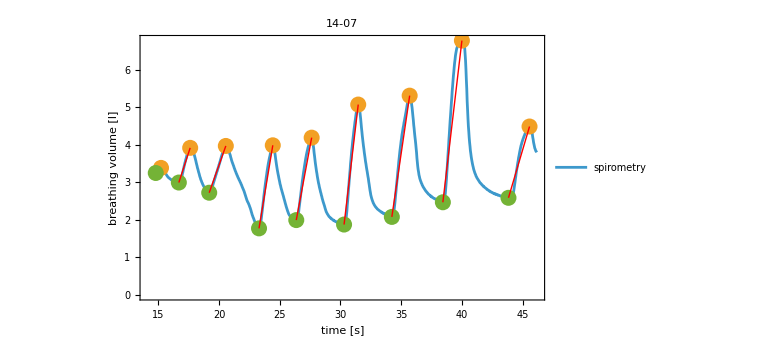
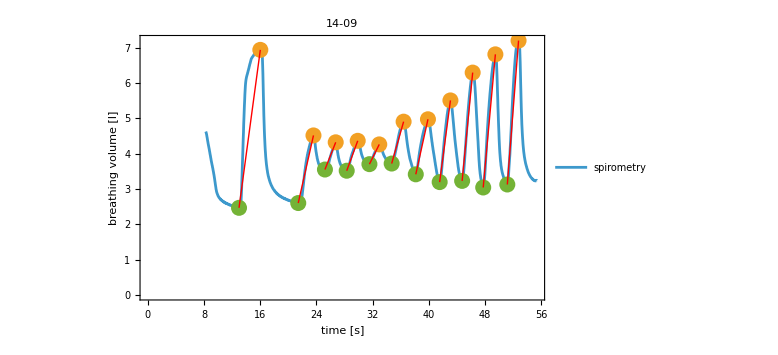
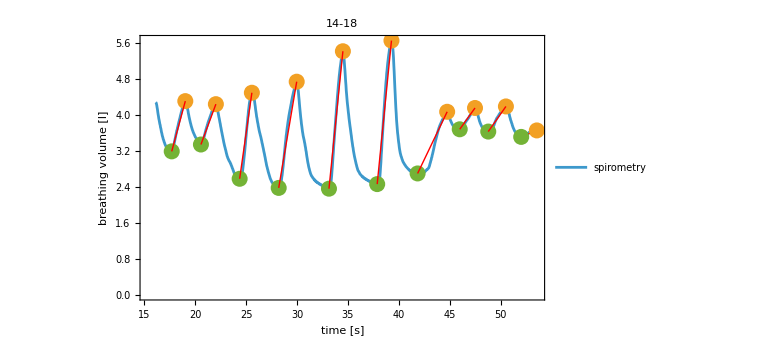
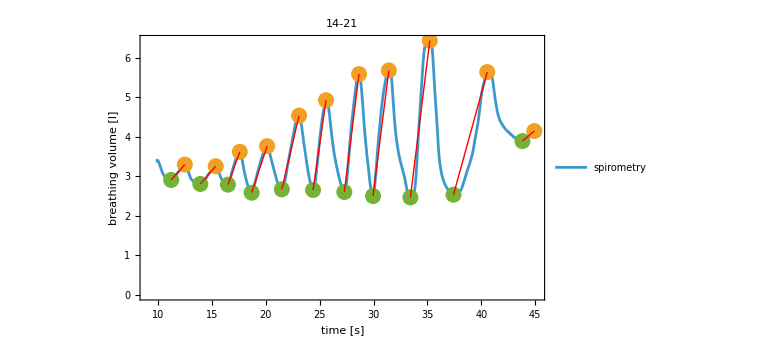

```mathematica
breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,values=l[[2,3]];
peaks=FindPeaks[l[[2,3]][[All,2]],10];
peaksLow=FindPeaks[-l[[2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}],

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],PlotLegends->{"spirometry"},FrameLabel->{"time [s]","breathing volume [l]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]}
]

spiroBreaths=breathDetect/@ dataForAnalysis
```

breaths from RIP

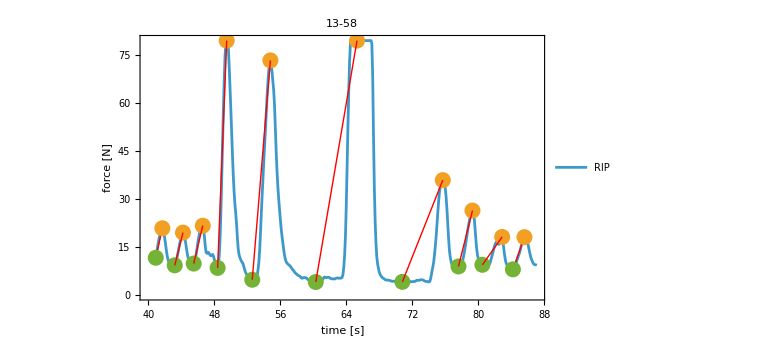
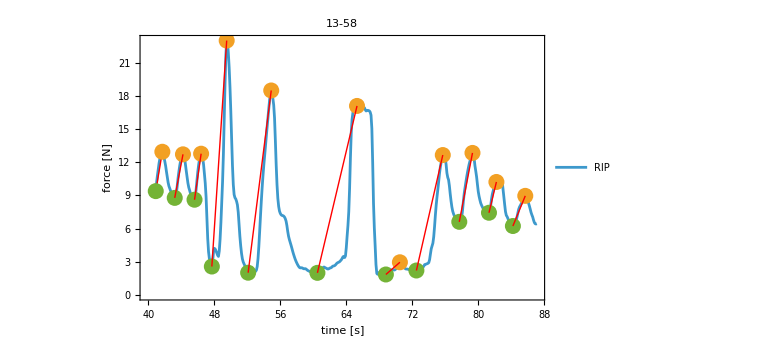
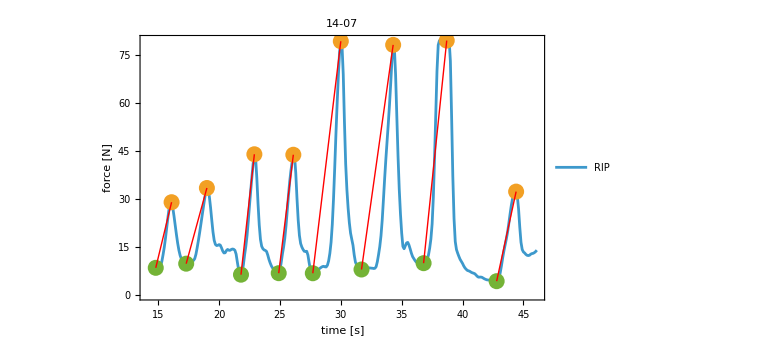
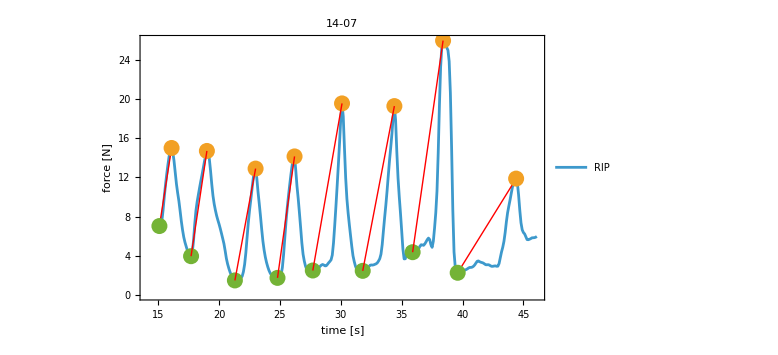
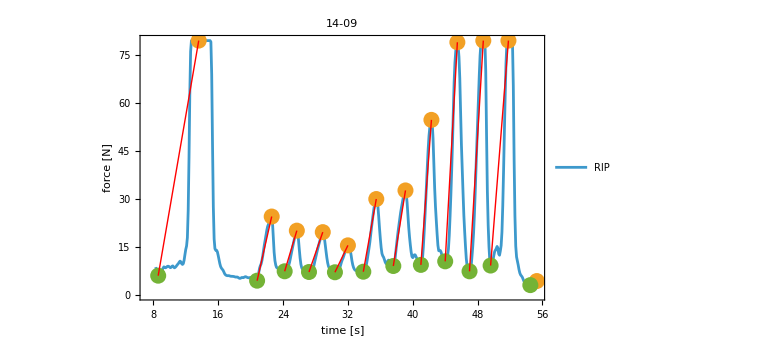
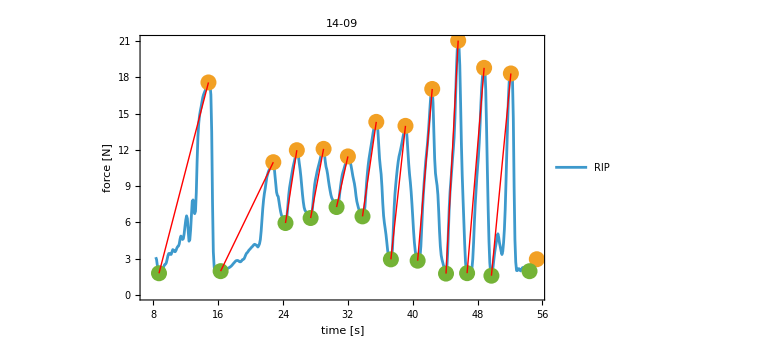
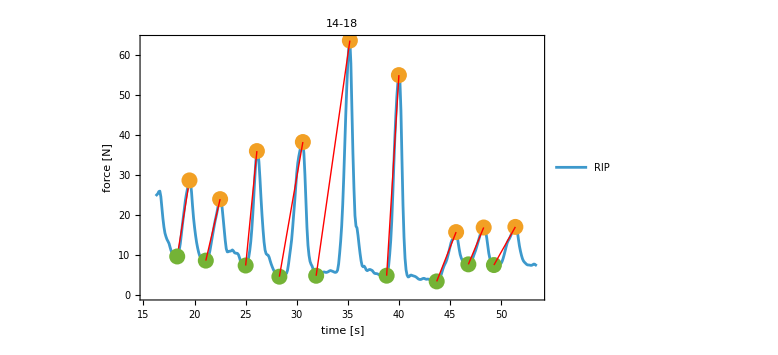
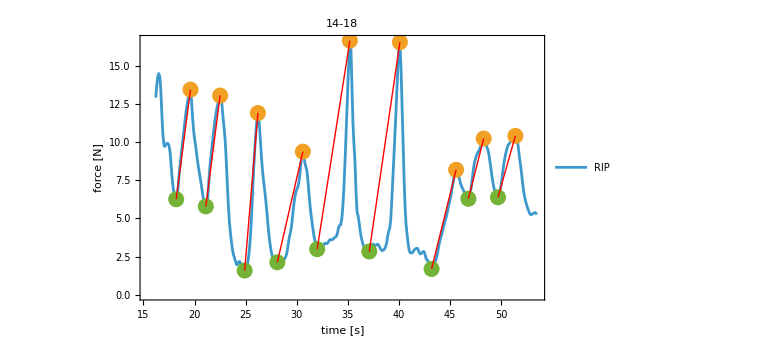

```mathematica
dataForAnalysisCropped=dataForAnalysis;
Table[
{lbound,ubound}=dataForAnalysisCropped[[i,2,3]][[{1,-1}]][[All,1]];
dataForAnalysisCropped[[i,2,1]]=Select[dataForAnalysisCropped[[i,2,1]],lbound<#[[1]]<ubound&];
dataForAnalysisCropped[[i,2,2]]=Select[dataForAnalysisCropped[[i,2,2]],lbound<#[[1]]<ubound&];
,{i,Length@dataForAnalysisCropped}];

breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,
Table[values=l[[2,i]];
peaks=FindPeaks[l[[2,i]][[All,2]],6];
peaksLow=FindPeaks[-l[[2,i]][[All,2]],6];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)
(*hier noch prüfen, ob der Peak im Zeitverlauf auch nahe am Peak der Spirometrie liegt!!! 10%?*)
peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ force [N]"}]
,Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],
PlotLegends->{"RIP"},FrameLabel->{"time [s]","force [N]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,PlotRange->All,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
}
,{i,{1,2}}]

]

ripBreaths=breathDetect/@dataForAnalysisCropped
```

```mathematica
Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]
```

{{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}}}

```mathematica
dCorrelation=Flatten/@Transpose[{spiroBreaths[[All,1]],ripBreaths[[All,All,1]]}]
```

{{,,},{,,},{,,},{,,},{,,}}

```mathematica
myTabularNormal=.
myTabularNormal[t_]:=Module[{},If[TabularQ[t],Values/@(Normal@t),Values/@(Normal/@t)]]
```

```mathematica
spiroBreaths[[1,2]]
```

-Graphics-

```mathematica
myPlotLabelAndLegend[plotLabel_,plotLegend_List,frameLabel_List]:=Sequence[PlotLabel->myStyle@plotLabel,
PlotLegends->myStyle/@plotLegend,FrameLabel->frameLabel]
```

```mathematica
myPlotConfig=.
myPlotConfig=Sequence[PlotRange->All,Frame->True,ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]
```

Sequence[PlotRange→All,Frame→True,ImageSize→Large,FrameStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]],FrameTicksStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]]]

```mathematica
myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP"},{"force [N]","breathing volume [l]"}]
```

Sequence[PlotLabel→13-58,PlotLegends→{correlation spirometry and RIP},FrameLabel→{force [N],breathing volume [l]}]

{10,10,10}

{{{1.3,0.8,0.8},{0.415254,9.22866,3.55912}},{{1.13333,1.,1.},{0.305085,10.2353,3.93726}},{{1.1,1.1,0.8},{0.525424,11.845,4.15954}},{{1.26667,1.1,1.8},{3.33898,71.1057,20.4221}},{{1.9,2.2,2.8},{3.0678,68.6171,16.4721}},{{3.6,5.,4.8},{4.41525,75.5309,15.0873}},{{2.26667,4.9,3.2},{2.67797,31.8302,10.4372}},{{1.6,1.7,1.6},{0.966102,17.4915,6.22909}},{{1.66667,2.4,0.9},{0.491525,8.71255,2.78239}},{{1.66667,1.4,1.5},{0.576271,10.0641,2.72619}}}

FittedModel[…]

{0.0659819+0.0512292 x-2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2),0.0659819+0.0512292 x+2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2)}

{,}

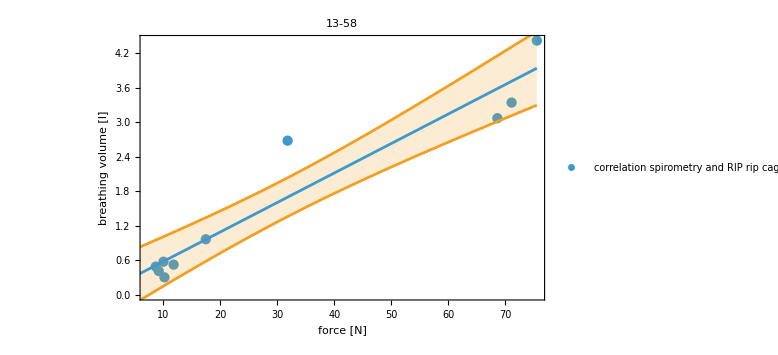

```mathematica
temp=myTabularNormal[dCorrelation[[1]]];
temp[[3]] = Select[temp[[3]],#[[2]]>1.5&];
Length/@temp
temp=Transpose/@Transpose[temp]
lnm=LinearModelFit[temp[[All,2]][[All,{2,1}]],x,x]
lnm["MeanPredictionBands",ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[temp[[All,2]][[All,{2,1}]],myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@temp[[All,2]][[All,{2,1}]],Max@temp[[All,2]][[All,{2,1}]]},Filling->{2->{1}}]]
```

manuelle Anpassung, siehe auch Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]

13 - 58 delete 7 bei abdomen
14-07 delete 1 bei spiro
14 - 09 delete - 1 bei cage und abdomen
14 - 18 delete - 1 bei spirometry
14-21 delete -1 bei spirometry und cage

```mathematica
evaluableData
```

{13-58,14-07,14-09,14-18,14-21}

```mathematica
dCorrelationElected=myTabularNormal/@dCorrelation;
dCorrelationElected=Delete[dCorrelationElected,{{1,3,7},{2,1,1},{3,2,-1},{3,3,-1},{4,1,-1},{5,1,-1},{5,2,-1}}];
Map[Length,dCorrelationElected,{2}]
dCorrelationElected=myFlatten[Transpose[dCorrelationElected][[All,All,All,2]],1];
```

{{10,10,10},{8,8,8},{11,11,11},{9,9,9},{10,10,10}}

FittedModel[…]

FittedModel[…]

{0.90628,0.904242}

0.156586

{{0.181881+0.0487349 x-2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2),0.181881+0.0487349 x+2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2)},}

{,}

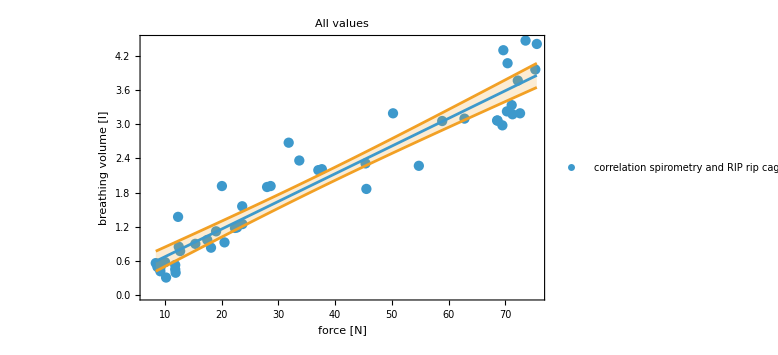

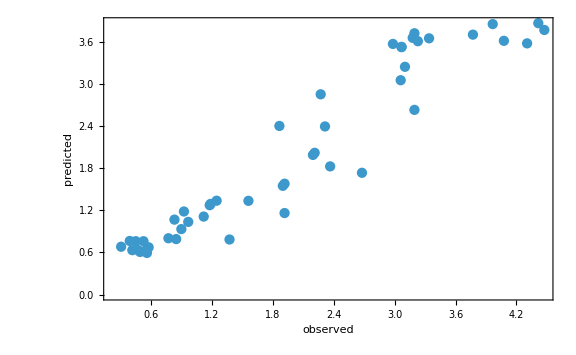

```mathematica
lnmRipCageGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,2}]]],x,x] (*volume in Newton out*)
fitData=Transpose[dCorrelationElected[[{2,1}]]];
lnmRipCageGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95] (*https://www.graphpad.com/support/faqid/1506/  Prediciton = wo die nächsten Datenpunkte mit 95% Wahrscheinlichkeit liegen werden, Confidence = wo die aktuellen Daten zu 95% liegen and https://en.wikipedia.org/wiki/Confidence_and_prediction_bands#Prediction_bands*)
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
Min@fitData[[All,1]]
```

8.41872

FittedModel[…]

FittedModel[…]

{0.773369,0.768442}

0.37865

{{-0.123767+0.187762 x-2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2),-0.123767+0.187762 x+2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2)},}

{,}

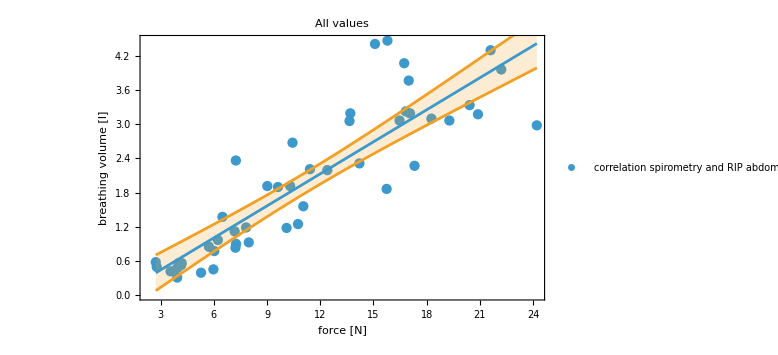

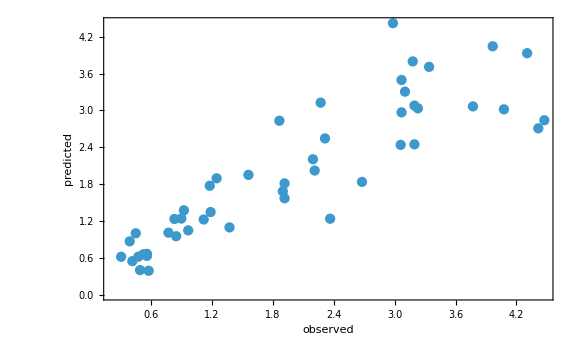

```mathematica
lnmAbdomenGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,3}]]],x,x]
fitData=Transpose[dCorrelationElected[[{3,1}]]];
lnmAbdomenGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP abdomen"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
newtonFromRIPripcage=.
newtonFromRIPripcage[v_]:=Module[{},Around[lnmRipCageGetForce[v],(Subtract@@Reverse@(lnmRipCageGetForce["MeanPredictionBands",ConfidenceLevel->.95] /. x->v))/2]]
{#,newtonFromRIPcage[#]}&/@{3,5}
```

{{3,newtonFromRIPcage[3]},{5,newtonFromRIPcage[5]}}

```mathematica
volumeFromRIPripcage=.
volumeFromRIPripcage[f_]:=Module[{},Around[lnmRipCageGetVolume[f],(Subtract@@Reverse@(lnmRipCageGetVolume["MeanPredictionBands",ConfidenceLevel->.95] /. x->f))/2]]
{#,newtonFromRIPcage[#]}&/@{20,40,60}
```

{{20,newtonFromRIPcage[20]},{40,newtonFromRIPcage[40]},{60,newtonFromRIPcage[60]}}

-Graphics--Graphics-
aus
 https://publikationen.dguv.de/widgets/pdf/download/article/1011%7CDGUV-Regel112-190_Benutzung-von-Atemschutzgeraeten_Download.pdf

Zielwerte: 30 und 50 l/min  Atemminutenvolumen

```mathematica
af=Range[10,70,5] (*Atemfrequenz*)
```

{10,15,20,25,30,35,40,45,50,55,60,65,70}

```mathematica
Print[myStyle["values for 30 l/min"]]
TableForm[{af,30./af,newtonFromRIPripcage/@(30./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 30 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 3. | 2. | 1.5 | 1.2 | 1. | 0.857143 | 0.75 | 0.666667 | 0.6 | 0.545455 | 0.5 | 0.461538 | 0.428571
force of RIP of ripcage [N] | 55.92.9 | 37.32.2 | 28.02.4 | 22.42.7 | 18.72.9 | 16.03.0 | 14.03.1 | 12.53.3 | 11.33.3 | 10.23.4 | 9.43.5 | 8.73.5 | 8.4.

```mathematica
Print[myStyle["values for 50 l/min"]]
TableForm[{af,50./af,newtonFromRIPripcage/@(50./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 50 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 5. | 3.33333 | 2.5 | 2. | 1.66667 | 1.42857 | 1.25 | 1.11111 | 1. | 0.909091 | 0.833333 | 0.769231 | 0.714286
force of RIP of ripcage [N] | 93.6. | 62.13.3 | 46.62.4 | 37.32.2 | 31.12.3 | 26.72.5 | 23.32.6 | 20.82.7 | 18.72.9 | 17.03.0 | 15.63.0 | 14.43.1 | 13.43.2

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 30 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[30,{#[[1]]-#[[2]]corr,#[[1]]+#[[2]]corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 30 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 50 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[50,{#[[1]]-#[[2]] corr,#[[1]]+#[[2]] corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 50 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate